```mathematica
SetDirectory[NotebookDirectory[]];ClearAll["Global`*"];
Get["../db/ETC.mx"];
Get["../sources/KimberlingPoints.m"];
Get["../sources/TriangleTools.m"];
Get["../sources/KimberlingTriangles.m"];
Get["../sources/TriangleExpressions.m"];
```

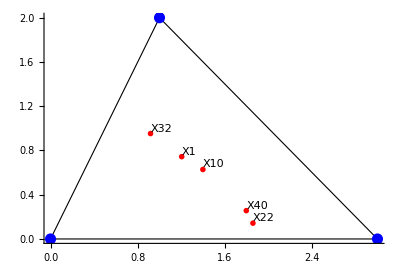

{(3 (1+√5))/(3+2 √2+√5),6/(3+2 √2+√5)}

{(9+8 √2+√5)/(6+4 √2+2 √5),(2 √2+√5)/(3+2 √2+√5)}

{13/7,1/7}

{78/85,81/85}

{(3 (-1+√5))/(-3+2 √2+√5),1/2 (-1+√2) (-1+√5)}

```mathematica
PA={0,0}; PB={3,0}; PC={1,2};
indices = {1,10,22, 32, 40};
centers =Table[KimberlingCenter[i,PA,PB,PC],{i,indices}]//Simplify;
names=Table["X"<>TextString[n],{n,indices}];
Graphics[Join[
{EdgeForm[{Thin, Black}], FaceForm[], Triangle[{PA,PB,PC}]},
{{PA, PB, PC}/.{x_,y_}:>{Blue,PointSize[0.02],Point[{x,y}]}},
{centers/.{x_,y_}:>{Red,PointSize[0.01],Point[{x,y}]}},
Text[#[[1]],#[[2]],-1.5 Sign@#[[2]]]&/@Transpose@{names, centers}
], AspectRatio->Automatic, Axes-> True
]
Print/@centers;
```